### Solve differential equations of population growth

#### Set constants

```mathematica
ClearAll[S0,R0,K,S,R,s,r,t,α,μ1,μ2]
S0=1*^3;
R0=1*^3;
K=1*^5;
```

#### Population growth equations - simple

```mathematica
(*solution = DSolve[{
S'[t]==μ1*S[t]-α*S[t],
R'[t]==μ2*R[t]+α*S[t]
},{S[t],R[t]},t];*)
```

#### Population growth equations - logistic growth

```mathematica
solution = ParametricNDSolve[{
S'[t]==μ1*(1-(S[t]+R[t])/K)*S[t]-α*S[t],
R'[t]==μ2*(1-(S[t]+R[t])/K)*R[t]+α*S[t],
S[0]==S0,R[0]==R0},
{S,R},
{t,0,25},
{μ1,μ2,α}]
```

{S→ParametricFunction[<>],R→ParametricFunction[<>]}

#### Assign equations to functions

```mathematica
s[t_]=S[t]/.solution;
r[t_]=R[t]/.solution;
```

#### Plot

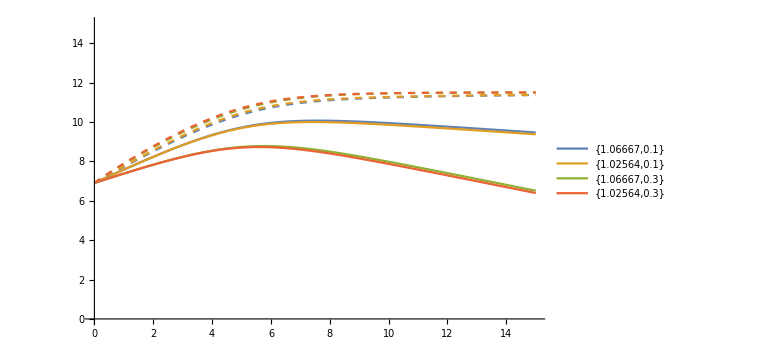

```mathematica
mu1={.8};
mu2={.75,.78};
alp={.1,.3};
tmax=15;

params=Join@@@Table[{m1/m2,α},{m1,mu1},{α,alp},{m2,mu2}];

Show[Plot[
Evaluate@Table[Log[S[μ1,μ2,α][t]]/.solution,
{μ1,mu1},{α,alp},{μ2,mu2}],
{t,0,tmax},
PlotStyle->Thick,
PlotLegends->{params},
PlotRange->{All,{0,15}}
],
Plot[
Evaluate@Table[Log[R[μ1,μ2,α][t]]/.solution,
{μ1,mu1},{α,alp},{μ2,mu2}],
{t,0,tmax},
PlotStyle->Dashed,
PlotRange->All],
ImageSize->Large]
```

```mathematica
(*Show[Plot[Evaluate@Table[{
Log[s[t,.8,μ2,α]],
Log[r[t,.8,μ2,α]]},
{μ2,{.75,.78}},{α,{.1,.3}}],
{t,1,20},
PlotLegends->{"S","R"},
AxesLabel->{{"t"},"Population"},
PlotStyle->Thick],ImageSize->Large]*)
```